```mathematica
f[x_] = 3 x x x-2x
```

-2 x+3 x^3

```mathematica
f[1]
```

1

```mathematica
f[2]
```

20

```mathematica
Clear[f]
```

```mathematica
f[1]
```

f[1]

```mathematica
f[x_, y_] = 3 x x x + 2y^2x + 4y*y
```

3 x^3+4 y^2+2 x y^2

```mathematica
Plot[f[x,y],{x,0,10},{y,0,10}]
```

Plot::nonopt: Options expected (instead of {y, 0, 10}) beyond position 2 in Plot[f[x, y], {x, 0, 10}, {y, 0, 10}]. An option must be a rule or a list of rules.

```mathematica
Plot3D[f[x,y],{x,0,10},{y,0,10}]
```

```mathematica
f[x_] = x x x - 3 x x - 9 x +1
```

1-9 x-3 x^2+x^3

```mathematica
f'
```

8 #1&

```mathematica
f'[x]
```

8 x

```mathematica
Plot[f[x],f'[x],{x,0,10}]
```

Plot::nonopt: Options expected (instead of {x, 0, 10}) beyond position 2 in f[x], SuperscriptBox[. An option must be a rule or a list of rules.

```mathematica
Plot[{f[x],f'[x]*(x-y)},{x,-10,10},{y,-10,10}]
```

Plot::nonopt: Options expected (instead of {y, -10, 10}) beyond position 2 in {f[x], SuperscriptBox[. An option must be a rule or a list of rules.

Plot[{f[x],f'[x] (x-y)},{x,-10,10},{y,-10,10}]

```mathematica
Plot[{f[x],f'[y]},{{x,0,20}, {y,0,10}}]
```

Plot::pllim: Range specification {{x, 0, 20}, {y, 0, 10}} is not of the form {x, xmin, xmax}.

```mathematica
ParametricPlot[{f[x],f'[y]},{{x,0,20},{y,0,10}}]
```

ParametricPlot::pllim: Range specification {{x, 0, 20}, {y, 0, 10}} is not of the form {x, xmin, xmax}.

```mathematica
ParametricPlot[{f[x],f'[y]},{x,0,20},{y,0,10}]
```

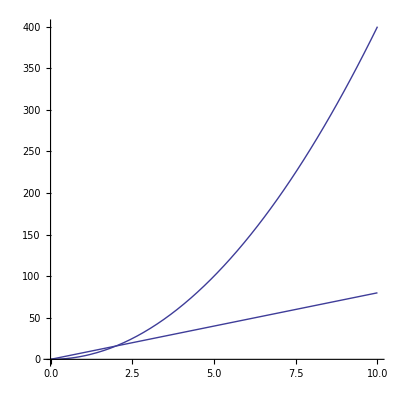

```mathematica
Show[Plot[f[x],{x,0,10}, AspectRatio-> 1], Plot[f'[y],{y,0,10},AspectRatio->Automatic]]
```

```mathematica
j[p_, x_] = f[p] + f'[p]*(x-p)
```

1-9 p-3 p^2+p^3+(-9-6 p+3 p^2) (-p+x)

```mathematica
f[x]
```

```mathematica
p1 = Plot[f[x],{x,-20,20}];
```

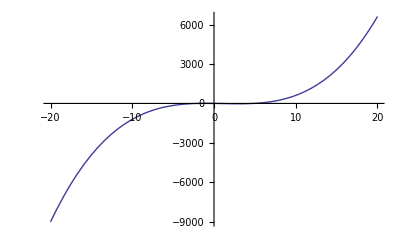

```mathematica
p1
```

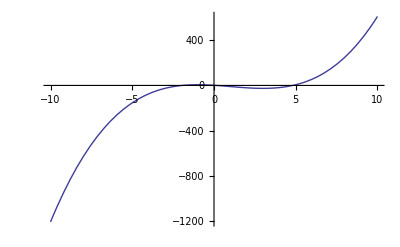

Show::gcomb: Could not combine the graphics objects in ….

```mathematica
p1
```

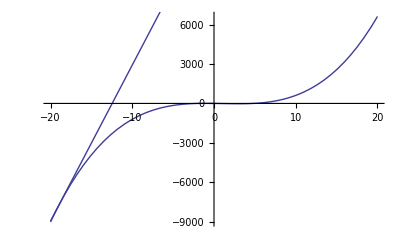

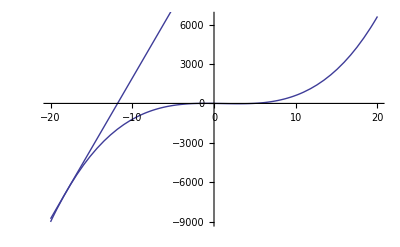

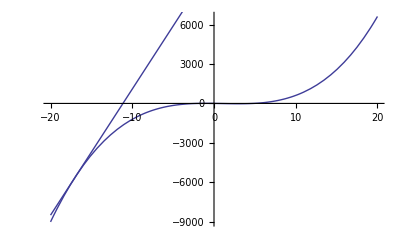

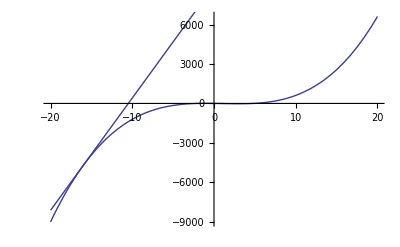

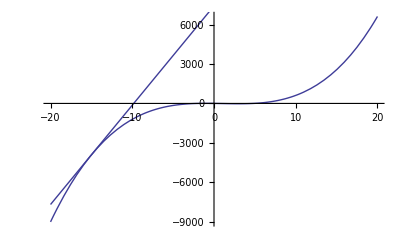

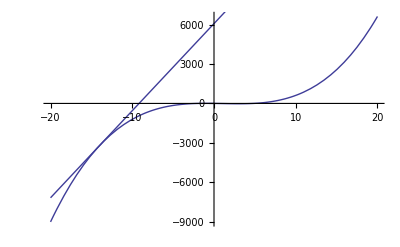

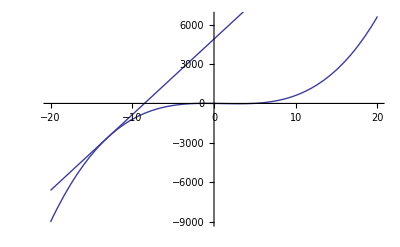

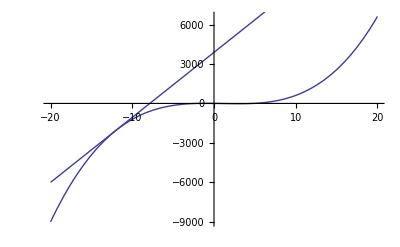

```mathematica
For[c=-20, c≤20, c++; Print[ Show[p1,  Plot[j[c,x],{x,-20,20}]]] ]
```

```mathematica
p1
```

-Graphics-